```mathematica
Manipulate[
Module[{di,Ac,P,ΔH,Ua,Ta,Cp,A,Ea,k,R,Q,r,Fao,To,Ti,s,Qloc,p1,p2,p3,p4,x1,x2,fQ},
di=0.25;(*m*)
Ac=(π/4)*di^2;
P=5;(*bar*)
ΔH=If[bn==1,-1,1]*75000;
Ua=500;
Ta=400;
Cp=75;
A=0.1;
Ea=1.16*10^4;
k[temp_]=A*Exp[-Ea/(8.314*(temp+273))];
R=8.314*10^-5;
Q[temp_]=(R*(temp+273))/P*(Fa[z]+Fb[z]);

Fao=0.5;
To=400;

s=NDSolve[{
Fa'[z]==-(k[T[z]]*Fa[z])/Q[T[z]]*Ac,
Fb'[z]==n*(k[T[z]]*Fa[z])/Q[T[z]]*Ac,
T'[z]==Ac*((-k[T[z]]*Fa[z]*Ac/Q[T[z]])*ΔH-Ua*(T[z]-Ta))/((Fa[z]+Fb[z])*Cp),
Fa[0]==Fao,Fb[0]==0,T[0]==To},{Fa,Fb,T},{z,-1,L+1}];

Qloc[loc_]=Q[T[z]]/.z->loc/.s[[1]];

p1=Plot[{Fa[z]/.s,Fb[z]/.s},{z,0,L},
PlotRange->{0,1.2},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.,0.6,0.06]}},
FrameLabel->{Style["distance down reactor (m)",16],Style["molar flow rate (mol/s)",16]}];

p2=Plot[T[z]/.s,{z,0,L},
PlotRange->If[bn==1,{400,407},{393,400}],
PlotStyle->{Thick,Black},
FrameLabel->{Style["distance down reactor (m)",16],Style["temperature (K)",16]}];

p3=Show[Plot[{Q[T[z]]/.s,Q[T[z]]/.z->0/.s},{z,0,L},
PlotRange->{0,0.0145},
PlotStyle->{{Thick,Black},{Thin,Black}},
FrameLabel->{Style["distance down reactor (m)",16],Style["volumetric flow rate (m^3/s)",16]}],
Graphics[{PointSize[0.02],Point[{location,Qloc[location]}]}]];

(*x1=Qloc[i]-Qloc[0];*)
fQ[Q1_,Q2_]=(Qloc[Q1]-Qloc[0])/(Qloc[Q2]-Qloc[0]);

(*x1=fQ[i-1,L-1]*Qloc[L];
x2=fQ[i,L-1]*Qloc[L];*)
(*x1=If[i==0,0,Qloc[i-1]];*)
x1=Qloc[i-1];
(*x2=Qloc[i]+(Qloc[i]-Qloc[0])+0.002;*)
(*x2=2*Qloc[i]-Qloc[0]+0.002;*)
x2=Qloc[i];

p4=Graphics[{
{Blue,Thick,Line[{{x1,0},{x1,0.1}}]},{Green,Thick,Line[{{x2,0},{x2,0.1}}]},
Text[Framed@Style[Grid[{{"x1 =",x1},{"x2 =",x2}}],15],{0.01,0.05},{1,0}]
(*Rectangle[{x1,0},{x2,0.1}]*)
},Frame->{{None,True},{True,None}},PlotRange->{{Qloc[0],Qloc[L]+(Qloc[L]-Qloc[0])+0.002},{0,0.1}},AspectRatio->1/3];

Show[Switch[cs,1,p1,2,p2,3,p3,4,p4],Frame->True,LabelStyle->{Black,13},ImageSize->400,(*ImagePadding->{{55,5},{50,10}},*)PlotLabel->Style[Qloc[location],15]]

],
Control[{{i,0,""},0,L,Trigger,AnimationRate->5,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Grid[{
{Control[{{cs,4,""},{1->"molar flow rate",2->"temperature",3->"volumetric flow rate",4->"reactor?"},Setter}]},
{Control[{{bn,1,""},{1->"exothermic",2->"endothermic"},Setter}]}
},Alignment->Left],
Control[{{n,1.5,"product reaction coefficient"},0.5,3,0.5,Appearance->"Labeled"}],
Control[{{L,25,"reactor length (m)"},1,25,0.1,Appearance->"Labeled"}],
Control[{{location,0,""},0,L,Appearance->"Labeled"}]
]
```

```mathematica
(*Grid[{
{Graphics[{Text@Style[
If[n==1,"A ⟶ B",Which[
n==0.5,Row[{"A ⟶ ",1/2," B"}],
n==1.5,Row[{"A ⟶ ",3/2," B"}],
n==2,"A ⟶ 2 B",
n==2.5,Row[{"A ⟶ ",5/2," B"}],
n==3,"A ⟶ 3 B"
]],17]},ImageSize->{200,50}]},
{Show[Switch[cs,1,p1,2,p2],Frame->True,LabelStyle->{Black,13},ImageSize->400,ImagePadding->{{55,5},{50,10}}]}
},Alignment->Center]*)
```

```mathematica
ImageDimensions[-Graphics-]
```

{360,360}

```mathematica
(*Grid[{
{Control[{{cs,2,""},{1->"molar flow rate",2->"temperature"},Setter}],
Control[{{bn,1,"reaction:"},{1->"exothermic",2->"endothermic"},Setter}]},
{Control[{{n,1,"product reaction coefficient"},1,3,0.5,Appearance->"Labeled"}]},
{Control[{{L,25,"reactor length (m)"},1,25,0.1,Appearance->"Labeled"}]}
},Alignment->Left]*)
```

```mathematica
(*{{A,0.1,"A"},0.01,00.1,0.01,Appearance->"Labeled"},
{{Ea,1.16*10^4,"Ea"},10,10^5,Appearance->"Labeled"},*)
```

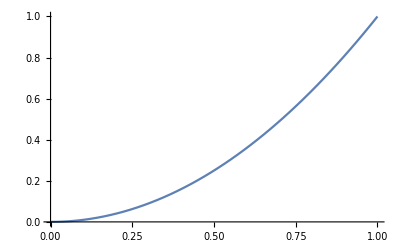

```mathematica
Plot[x^2,{x,0,1},PlotLabel->Graphics[{Text@Style[Row[{1/2," x"}],17]},ImageSize->{50,40}]]
```

```mathematica
Manipulate[
Sw
```